```mathematica
Clear["Global`*"];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/stasya/prj/pyBBN/tests/standard_model_bbn

#### Elecrton neutrinos

```mathematica
rawlinesEl = Import["./output/Electron_neutrino.distribution.txt", {"Text", "Lines"}][[2;; ]];
```

```mathematica
linesEl = StringSplit/@rawlinesEl[[2;;]];
linesEl = Map[Read[StringToStream[#],Number]&, linesEl, {2}];
```

```mathematica
T= Last[linesEl][[2]];
distEl1=Last[linesEl][[3;;]];
yEl=Map[Read[StringToStream[#],Number]&,StringSplit[rawlinesEl[[1]]][[4;;]]];
plotDataEl=Transpose[{yEl, distEl1}];
```

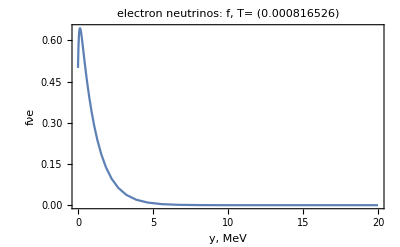

```mathematica
ListLinePlot[plotDataEl,PlotLabel->Style[#,Bold,15]&/@{"electron neutrinos: f, T= "@T},Frame-> True, FrameLabel->{"y, MeV","fνe"},PlotRange->All]
```

#### Muon neutrinos

```mathematica
rawlinesμ = Import["./output/Muon_neutrino.distribution.txt", {"Text", "Lines"}][[2;; ]];
```

```mathematica
linesμ = StringSplit/@rawlinesμ[[2;;]];
linesμ = Map[Read[StringToStream[#],Number]&, linesμ, {2}];
```

```mathematica
Tμ= Last[linesμ][[2]];
distμ=Last[linesμ][[3;;]];
yμ=Map[Read[StringToStream[#],Number]&,StringSplit[rawlinesμ[[1]]][[4;;]]];
plotDataμ=Transpose[{yμ, distμ}];
```

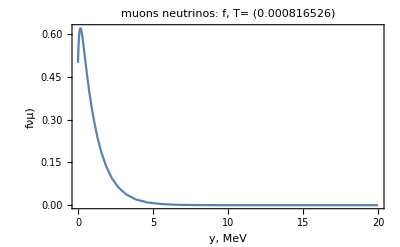

```mathematica
ListLinePlot[plotDataμ,PlotLabel->Style[#,Bold,15]&/@{"muons neutrinos: f, T= "@T},Frame-> True, FrameLabel->{"y, MeV","fνμ)"},PlotRange->All]
```

## Final spectrum. Comparison with previous results (Fig. 10)

```mathematica
(*final-spectra-SM.eps*)
multiplier={#⟦1⟧,#⟦2⟧*(Exp[#⟦1⟧]+1)}&;
(*finalspectraSMTest2015Electron =multiplier/@Import["../tests/standard_model_bbn/spectrum_Electron neutrino.dat","HeaderLines"->1];
finalspectraSMTest2015ElectronFunc = Interpolation[finalspectraSMTest2015Electron];
finalspectraSMTest2015Muon = multiplier/@Import["../tests/standard_model_bbn/spectrum_Muon neutrino.dat","HeaderLines"->1];
finalspectraSMTest2015MuonFunc = Interpolation[finalspectraSMTest2015Muon];*)
```

```mathematica
plotfEl=Interpolation[multiplier/@plotDataEl];
plotfμ=Interpolation[multiplier/@plotDataμ];
```

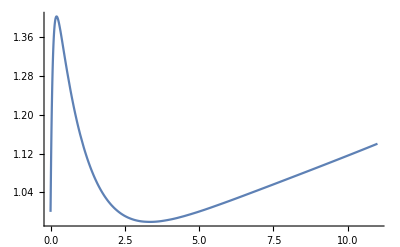

```mathematica
Plot[plotfEl[y],{y,0,11}]
```

```mathematica
finalspectraSMTest=Import["../../figures/Figures-sources/Final-spectra-SM/spectra-test-SM.dat","HeaderLines"->3];
```

```mathematica
finalspectranueSMDigit=Import["../../figures/Figures-sources/Final-spectra-SM/Mangano-nue-noosc.tsv"];
finalspectranumuSMDigit=Import["../../figures/Figures-sources/Final-spectra-SM/Mangano-numu-noosc.tsv"];
```

```mathematica
finalnueSMTestFunc=Interpolation[multiplier/@finalspectraSMTest[[All,{1,4}]]];
finalnumuSMTestFunc=Interpolation[multiplier/@finalspectraSMTest[[All,{1,8}]]];
```

```mathematica
finalspectranueSMDigitFunc=Interpolation[finalspectranueSMDigit[[All,{1,2}]]];
finalspectranumuSMDigitFunc=Interpolation[finalspectranumuSMDigit[[All,{1,2}]]];
```

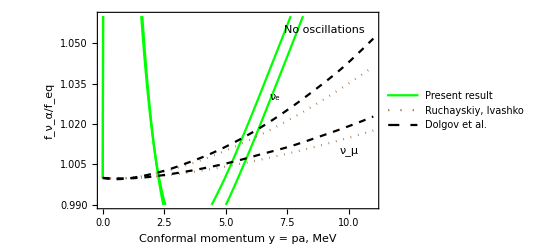

$Aborted

```mathematica
plt=Plot[{
plotfEl[y],
plotfμ[y],
finalnueSMTestFunc[y],
finalnumuSMTestFunc[y],
finalspectranueSMDigitFunc[y],
finalspectranumuSMDigitFunc[y]
},{y,0,11},PlotRange->{{0,11},{0.99,1.06}},Frame->True,FrameLabel->{"Conformal momentum y = pa, MeV","f_ν_α/f_eq"},PlotStyle->{{Green},{Green},{Brown,Dotted},{Brown,Dotted},{Black,Dashed},{Black,Dashed}},Epilog->{Text["ν_e",{7,1.03}],Text["ν_μ",{10,1.01}],Text["No oscillations",{9,1.055}]},
PlotLegends->{"Present result",None,"Ruchayskiy, Ivashko",None,"Dolgov et al.",None}]
Export["Figures-sources/final-spectra-SM-noosc.eps",%];
```

## Final spectrum. Comparison with previous results (Fig. 11)

### Electron neutrinos

```mathematica
aEl=First[Transpose[linesEl]];
```

```mathematica
setofdistributionsEl=Transpose[Transpose[linesEl][[3 ;;]]];
```

```mathematica
interpolatedDistEl=Interpolation/@setofdistributionsEl;
```

```mathematica
f3El=Interpolation[Transpose[{aEl,#[3]&/@interpolatedDistEl}]];
f5El=Interpolation[Transpose[{aEl,#[5]&/@interpolatedDistEl}]];
f7El=Interpolation[Transpose[{aEl,#[7]&/@interpolatedDistEl}]];
```

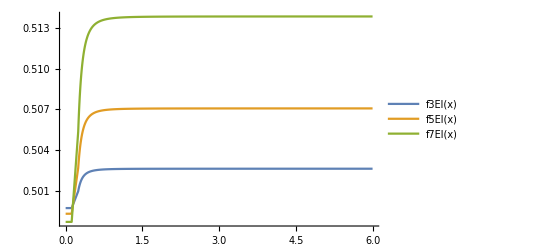

```mathematica
Plot[{f3El[x],f5El[x],f7El[x]},{x,0,6},PlotLegends->"Expressions"]
```

$Aborted

$Aborted

$Aborted

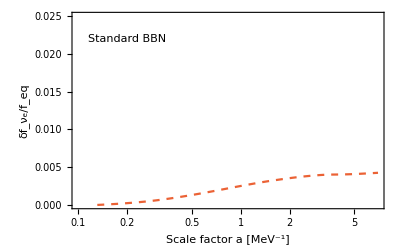

```mathematica
(*sm-deltafnue_comp.eps*)
deltafnue3Digit=Import["../../figures/Figures-sources/sm-deltafnue_comp/sm-dfnue3-semi.dat","HeaderLines"->1];
deltafnue5Digit=Import["../../figures/Figures-sources/sm-deltafnue_comp/sm-dfnue5-semi.dat","HeaderLines"->1];
deltafnue7Digit=Import["../../figures/Figures-sources/sm-deltafnue_comp/sm-dfnue7-semi.dat","HeaderLines"->1];

deltafnue3DigitFunc=Interpolation[deltafnue3Digit[[All,{1,2}]],InterpolationOrder->2,Method->"Spline"];
deltafnue5DigitFunc=Interpolation[deltafnue5Digit[[All,{1,2}]],InterpolationOrder->2,Method->"Spline"];
deltafnue7DigitFunc=Interpolation[deltafnue7Digit[[All,{1,2}]],InterpolationOrder->2,Method->"Spline"];

LogLinearPlot[{f3El[x]*(Exp[3]+1)-1,f5El[x]*(Exp[5]+1)-1,f7El[x]*(Exp[7]+1)-1,deltafnue3DigitFunc[x],deltafnue5DigitFunc[x],deltafnue7DigitFunc[x]},{x,0.1,7},PlotRange->{{0.1,7},{0,0.025}},Frame->True,FrameLabel->{"Scale factor a [MeV^-1]","δf_ν_e/f_eq"},PlotStyle->{{},{},{},{Dashed},{Dashed},{Dashed}},Epilog->{Text["Standard BBN",{Log[0.2],0.022}]}]
```

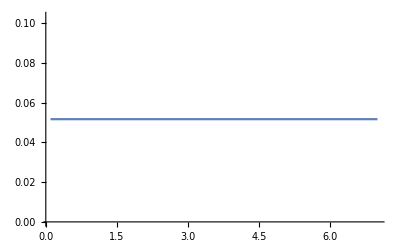

```mathematica
Plot[f3El[x]*(Exp[0.5/T]+1)-1,{x,0.1,7}]
```